## Nicolas’s Testing Ground

```mathematica
point1[x_]:=Module[{},
If[x≤5,{x,x},{x,10-x}]];
Animate[Graphics[Point[point1[t]],Axes->True,AspectRatio->Automatic, PlotRange->{{0,15},{0,15}}],{t,0,10}]
(*To Test animating an If statement*)
```

```mathematica
p=Plot[Sin[x],{x,-Pi,Pi}];
Animate[Show[p,Graphics[Point[{a,Sin[a]}]]],{a,-1,1}]
(*Suggestion given by the professor on how to format the combined plot and graphic. This one uses a Plot command though and not a parametric plot*)
```

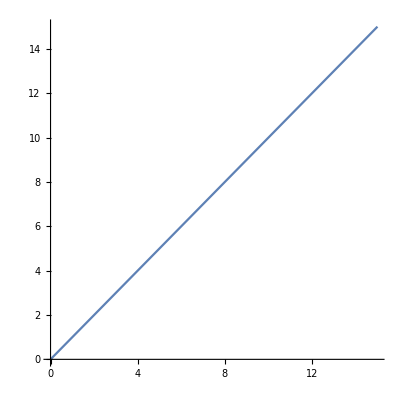

```mathematica
p2=ParametricPlot[{t,t},{t,0,15}]
Animate[Show[p2,Graphics[Point[{a,a}],Axes->True,AspectRatio->Automatic, PlotRange->{{0,15},{0,15}}]],{a,0,10}]
```

```mathematica
(*So it worked for a parametric plot. I'm guessing that there was a problem in the nesting of the two functions between Animate, Show, and Graphic
```

```mathematica
r={1,5};
r.r
```

26

```mathematica
{4,35}-6
```

{-2,29}

```mathematica
twoStageorbit[thrustx_,thrusty_,timeThrustApplied_,mass_]:= Module[
{massEarth,radiusEarth,centerOfEarth,bigG,fGravity,r,rUnitvector,force,acc,vel,pos,t},
(*Define the constants*)
massEarth=5.97219 10^24;
radiusEarth=6378.1 10^3;
centerOfEarth={0,0};
bigG=-6.67430 10^-11;
rUnitvector=Normalize[pos];
fGravity:=rUnitvector mass bigG massEarth/(pos^2);
force[t_]={thrustx,thrusty}+fGravity;

acc[t_]=force[t]/mass;
vel[t_]={0,0}+Integrate[acc[t],t]; (*No initial velocity*)
pos[t_]={0,radiusEarth}+Integrate[vel[t],t];

(*set up the parametric plot for thrust stage*)
thrustPlot=ParametricPlot[pos[t],{t,0,timeThrustApplied},PlotStyle->{Blue, Dashed}];
```

```mathematica
k={4,5}
Normalize[k]
```

{4,5}

{4/(√41),5/(√41)}

```mathematica
massEarth=5.97219 10^24;
radiusEarth=6378.1 10^3;
centerOfEarth={0,0};
bigG=-6.67430 10^-11;
rUnitvector=Normalize[pos[t]];
fGravity[t_]=rUnitvector 1000 bigG massEarth/(pos[t]^2);
force[t_]={1000,1000}+fGravity[t];

acc[t_]=force[t]/1000;
vel[t_]={0,0}+Integrate[acc[t],t]; (*No initial velocity*)
pos[t_]={0,radiusEarth}+Integrate[vel[t],t];
pos[10]
```

Set::write: Tag List in {-(3.98602×10^14 ∫(∫(1000+{-3.98602×10^14 Power[«2»] Power[«2»] Integrate[«2»],-3.98602×10^17 Power[«2»] Power[«2»] Plus[«2»]}[t])ⅆt)ⅆt)/(pos^2 √(Abs[6.3781×10^6+Times[«2»]]^2+Abs[Integrate[«2»]]^2/1000000)),-(3.98602×10^17 (6.3781×10^6+(∫(∫«1»)ⅆt)/1000))/(pos^2 √(Abs[6.3781×10^6+«1»]^2+(«1»)^2/1000000))}[t_] is Protected.

$Aborted

Integrate::ilim: Invalid integration variable or limit(s) in 10.

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

{1/1000(∫(∫(1000+{-((3.98602×10^14 ∫(∫(1000+{-(1.99301×10^16 force)/(pos^2 √(Abs[6.3781×10^6+force/20]^2+Abs[force]^2/400)),-(3.98602×10^17 (6.3781×10^6+force/20))/(pos^2 √(Abs[6.3781×10^6+force/20]^2+Abs[force]^2/400))}[10])ⅆ10)ⅆ10)/(pos^2 √(Abs[6.3781×10^6+1/1000(∫(∫(1000+{-(1.99301×10^16 force)/(pos^2 √(Abs[6.3781×10^6+force/20]^2+Abs[force]^2/400)),-(3.98602×10^17 (6.3781×10^6+force/20))/(pos^2 √(Abs[6.3781×10^6+force/20]^2+Abs[force]^2/400))}[10])ⅆ10)ⅆ10)]^2+1/1000000 Abs[∫(∫(1000+{-(1.99301×10^16 force)/(pos^2 √(Abs[6.3781×10^6+force/20]^2+Abs[force]^2/400)),-(3.98602×10^17 (6.3781×10^6+force/20))/(pos^2 √(Abs[6.3781×10^6+force/20]^2+Abs[force]^2/400))}[10])ⅆ10)ⅆ10]^2))),-((3.98602×10^17 (6.3781×10^6+1/1000(∫(∫(1000+{-(1.99301×10^16 force)/(pos^2 √(Abs[6.3781×10^6+force/20]^2+Abs[force]^2/400)),-(3.98602×10^17 (6.3781×10^6+force/20))/(pos^2 √(Abs[6.3781×10^6+force/20]^2+Abs[force]^2/400))}[10])ⅆ10)ⅆ10)))/(pos^2 √(Abs[6.3781×10^6+1/1000(∫(∫(1000+{-(1.99301×10^16 force)/(pos^2 √(Abs[6.3781×10^6+force/20]^2+Abs[force]^2/400)),-(3.98602×10^17 (6.3781×10^6+force/20))/(pos^2 √(Abs[6.3781×10^6+force/20]^2+Abs[force]^2/400))}[10])ⅆ10)ⅆ10)]^2+1/1000000 Abs[∫(∫(1000+{-(1.99301×10^16 force)/(pos^2 √(Abs[6.3781×10^6+force/20]^2+Abs[force]^2/400)),-(3.98602×10^17 (6.3781×10^6+force/20))/(pos^2 √(Abs[6.3781×10^6+force/20]^2+Abs[force]^2/400))}[10])ⅆ10)ⅆ10]^2)))}[10])ⅆ10)ⅆ10),6.3781×10^6+1/1000(∫(∫(1000+{-((3.98602×10^14 ∫(∫(1000+{-(1.99301×10^16 force)/(pos^2 √(Abs[6.3781×10^6+force/20]^2+Abs[force]^2/400)),-(3.98602×10^17 (6.3781×10^6+force/20))/(pos^2 √(Abs[6.3781×10^6+force/20]^2+Abs[force]^2/400))}[10])ⅆ10)ⅆ10)/(pos^2 √(Abs[6.3781×10^6+1/1000(∫(∫(1000+{-(1.99301×10^16 force)/(pos^2 √(Abs[6.3781×10^6+force/20]^2+Abs[force]^2/400)),-(3.98602×10^17 (6.3781×10^6+force/20))/(pos^2 √(Abs[6.3781×10^6+force/20]^2+Abs[force]^2/400))}[10])ⅆ10)ⅆ10)]^2+1/1000000 Abs[∫(∫(1000+{-(1.99301×10^16 force)/(pos^2 √(Abs[6.3781×10^6+force/20]^2+Abs[force]^2/400)),-(3.98602×10^17 (6.3781×10^6+force/20))/(pos^2 √(Abs[6.3781×10^6+force/20]^2+Abs[force]^2/400))}[10])ⅆ10)ⅆ10]^2))),-((3.98602×10^17 (6.3781×10^6+1/1000(∫(∫(1000+{-(1.99301×10^16 force)/(pos^2 √(Abs[6.3781×10^6+force/20]^2+Abs[force]^2/400)),-(3.98602×10^17 (6.3781×10^6+force/20))/(pos^2 √(Abs[6.3781×10^6+force/20]^2+Abs[force]^2/400))}[10])ⅆ10)ⅆ10)))/(pos^2 √(Abs[6.3781×10^6+1/1000(∫(∫(1000+{-(1.99301×10^16 force)/(pos^2 √(Abs[6.3781×10^6+force/20]^2+Abs[force]^2/400)),-(3.98602×10^17 (6.3781×10^6+force/20))/(pos^2 √(Abs[6.3781×10^6+force/20]^2+Abs[force]^2/400))}[10])ⅆ10)ⅆ10)]^2+1/1000000 Abs[∫(∫(1000+{-(1.99301×10^16 force)/(pos^2 √(Abs[6.3781×10^6+force/20]^2+Abs[force]^2/400)),-(3.98602×10^17 (6.3781×10^6+force/20))/(pos^2 √(Abs[6.3781×10^6+force/20]^2+Abs[force]^2/400))}[10])ⅆ10)ⅆ10]^2)))}[10])ⅆ10)ⅆ10)}